```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## Self-energy corrections to effective vertex

in total: 3 Particles insertions

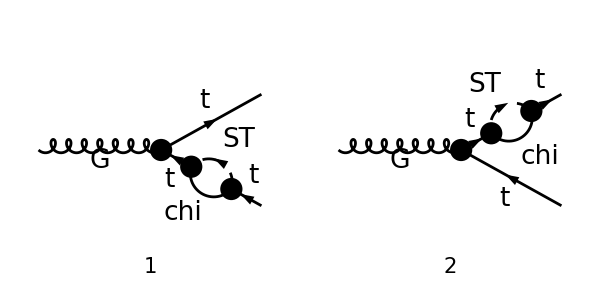

```mathematica
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processGGT =  {V[4]}->  {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[4],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8]}];
goodDiags=DiagramExtract[allDiags,{2,3}];
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0,SUNTF[a__]->1}
```

in total: 2 Particles amplitudes

-(ⅈ yDM^2 (γ̄)^7.(mChi-γ·q).(γ̄)^6.(MT+γ·p1).(ⅈ gs γ^μ.(γ̄)^6+ⅈ gs γ^μ.(γ̄)^7))/((p1^2-MT^2) (q^2-mChi^2).((p1+q)^2-mST^2))-(ⅈ yDM^2 (ⅈ gs γ^μ.(γ̄)^6+ⅈ gs γ^μ.(γ̄)^7).(MT-γ·p2).(γ̄)^7.(mChi+γ·q).(γ̄)^6)/((p2^2-MT^2) (q^2-mChi^2).((p2+q)^2-mST^2))

```mathematica
ampC =FeynAmpDenominatorExplicit[( TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True])]//Simplify
```

-ⅈ π^2 gs yDM^2 (((MT (γ·p1).γ^μ.(γ̄)^7+(γ·p1).(γ·p1).γ^μ.(γ̄)^6) B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)+((MT γ^μ.(γ·p2).(γ̄)^6-γ^μ.(γ·p2).(γ·p2).(γ̄)^6) B_1(p2^2,mChi^2,mST^2))/(MT^2-p2^2))

## g-g- t- t (1-loop - self energy)

```mathematica
topsL = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGTT = { V[4],V[4]} -> {F[9],-F[9]};
allDiagsL = InsertFields[topsL,processGGTT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

in total: 57 Particles insertions

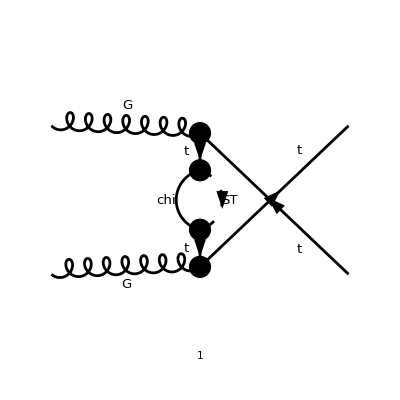

```mathematica
goodDiagsL=DiagramExtract[allDiagsL,{56}];
Paint[goodDiagsL,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampAL=FCFAConvert[CreateFeynAmp[goodDiagsL,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{pb,pa},LorentzIndexNames->{b,a},OutgoingMomenta->{p+pa,k2},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0,SUNTF[a__]->1}
```

in total: 1 Particles amplitude

(yDM^2 (ⅈ gs γ^a.(γ̄)^6+ⅈ gs γ^a.(γ̄)^7).(MT+γ·p).(γ̄)^7.(mChi+γ·q).(γ̄)^6.(MT+γ·p).(ⅈ gs γ^b.(γ̄)^6+ⅈ gs γ^b.(γ̄)^7))/((p^2-MT^2)^2 (q^2-mChi^2).((q-p)^2-mST^2))

```mathematica
(* 1/(2 p^2) ((mChi^2-mST^2+p^3)B0 -A0(mChi^2)+A0(mST^2)) = -B1(p^2) *)
```

```mathematica
ampCL =FullSimplify[DiracSimplify[FeynAmpDenominatorExplicit[( TID[ampAL,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])]]]
```

-(ⅈ π^2 gs^2 yDM^2 (MT^2 γ^a.(γ·p).γ^b.(γ̄)^7+p^2 (MT (γ^a.γ^b.(γ̄)^6+γ^a.γ^b.(γ̄)^7)+γ^a.(γ·p).γ^b.(γ̄)^6)) ((mChi^2-mST^2+p^2) B_0(p^2,mChi^2,mST^2)-A_0(mChi^2)+A_0(mST^2)))/(2 p^2 (MT^2-p^2)^2)

## Amplitude using the effective vertex

```mathematica
(* There are 2 vertex insertions and we remove the contribution from self-energy corrections to the external legs setting the appropriate B1 functions to zero *)
ampEffA1=I gs DiracGamma[LorentzIndex[a,D],D].((I (DiracGamma[Momentum[p,D],D]+MT))/(Pair[Momentum[p,D],Momentum[p,D]]-MT^2)).(ampC/.{p1->p,μ->b,PaVe[1,{Pair[Momentum[p2,D],Momentum[p2,D]]},__]->0})
ampEffA2=I gs (ampC/.{p2->-p,μ->a,PaVe[1,{Pair[Momentum[p1,D],Momentum[p1,D]]},__]->0}).((I (DiracGamma[Momentum[p,D],D]+MT))/(Pair[Momentum[p,D],Momentum[p,D]]-MT^2)).DiracGamma[LorentzIndex[b,D],D]
```

ⅈ gs γ^a.(ⅈ (MT+γ·p))/(p^2-MT^2).(-(ⅈ π^2 gs yDM^2 (MT (γ·p).γ^b.(γ̄)^7+(γ·p).(γ·p).γ^b.(γ̄)^6) B_1(p^2,mChi^2,mST^2))/(p^2-MT^2))

ⅈ gs (-(ⅈ π^2 gs yDM^2 (MT γ^a.(-(γ·p)).(γ̄)^6-γ^a.(-(γ·p)).(-(γ·p)).(γ̄)^6) B_1(p^2,mChi^2,mST^2))/(MT^2-p^2)).(ⅈ (MT+γ·p))/(p^2-MT^2).γ^b

```mathematica
ampEffA=FullSimplify[DiracSimplify[(ampEffA1+ampEffA2)]]/.{PaVe[1,a_,b_,c__]->B1[a[[1]],b[[1]],b[[2]]]}
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification b⟦1⟧ is longer than depth of object.

Part::partd: Part specification b⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(2 ⅈ π^2 gs^2 yDM^2 (MT^2 γ^a.(γ·p).γ^b.(γ̄)^7+p^2 (MT (γ^a.γ^b.(γ̄)^6+γ^a.γ^b.(γ̄)^7)+γ^a.(γ·p).γ^b.(γ̄)^6)) (-((mChi^2-mST^2+p^2) B_0(p^2,mChi^2,mST^2))/(2 p^2)+(A_0(mChi^2))/(2 p^2)-(A_0(mST^2))/(2 p^2)))/((MT^2-p^2)^2)

```mathematica
(* We see that there is indeed a double counting from using the effctive vertex to compute the t-channel self-energy corrections: *)
```

```mathematica
FullSimplify[ampEffA/2-ampCL]
```

0